### Loading Personality Feature Directions

```mathematica
path="/Users/rumiallbert/Desktop/Wolfram/Project/data/activations/";
```

```mathematica
SetDirectory[path];
```

```mathematica
files=FileNames["*_mean_of_diff_llama3.npy"];
```

```mathematica
pythonSession=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[pythonSession,"
import numpy as np
"]
```

```mathematica
loadFile[filename_]:=ExternalEvaluate[pythonSession,"
data = np.load('"<>path<>filename<>"', allow_pickle=True)
data.tolist()
"]
```

```mathematica
allPersMeanOfDiff=loadFile/@files;
```

```mathematica
personalityNames=StringReplace[StartOfString~~x:Shortest[__]~~"_"~~___~~EndOfString:>x]/@files;
```

```mathematica
Dimensions[allPersMeanOfDiff]
```

{156,31,4096}

```mathematica
(*Association[Thread[personalityNames->allPersMeanOfDiff]]*)
```

```mathematica
(*Transpose[{personalityNames,allPersMeanOfDiff}]*)
```

```mathematica
(*Thread[{personalityNames,allPersMeanOfDiff}]*)
```

```mathematica
Dimensions[allPersMeanOfDiff[[All,18]]]
```

{156,4096}

```mathematica
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"PrincipalComponentsAnalysis"]
reducerUMAP=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"UMAP"]
reducerTSNE=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"TSNE"]
(*Reduced Dimensions*)
reducedPCA=reducerPCA/@allPersMeanOfDiff[[All,18]];
reducedUMAP=reducerUMAP/@allPersMeanOfDiff[[All,18]];
reducedTSNE=reducerTSNE/@allPersMeanOfDiff[[All,18]];
```

DimensionReducerFunction[…]

DimensionReducerFunction[…]

DimensionReducerFunction[…]

```mathematica
(*Sample 50 personalities*)
sampleSize=50;
sampleIndices=RandomSample[Range[Length[personalityNames]],sampleSize];

sampledPersonalityNames=personalityNames[[sampleIndices]];
sampledReducedPCA=reducedPCA[[sampleIndices]];
sampledReducedUMAP=reducedUMAP[[sampleIndices]];
sampledReducedTSNE=reducedTSNE[[sampleIndices]];

(*Define the individual plots with larger ImageSize and no axis tick marks*)
plotPCA=ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedPCA,sampledPersonalityNames}],ImageSize->400,PlotLegends->sampledPersonalityNames,PlotLabel->"PCA",Axes->False];

plotUMAP=ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedUMAP,sampledPersonalityNames}],ImageSize->500,PlotLabel->"UMAP",Axes->False];

plotTSNE=ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedTSNE,sampledPersonalityNames}],ImageSize->500,PlotLabel->"t-SNE",Axes->False];

(*Combine them into a grid with reduced spacing*)
GraphicsGrid[{{plotPCA,plotUMAP,plotTSNE}},Spacings->{1,1},ImageSize->1300,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{2,{Automatic,{1->-90}}}]
```

-Graphics-

```mathematica
reducerTSNE=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"TSNE"]
reducedTSNE=reducerTSNE/@allPersMeanOfDiff[[All,18]];
ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedTSNE,sampledPersonalityNames}],ImageSize->1000,PlotLabel->"t-SNE",Axes->False]
```

DimensionReducerFunction[…]

-Graphics-

```mathematica
(*get the top words for top PCA values*)
```

```mathematica
(*Perform k-means clustering with 15 clusters*)
clusters=ClusteringComponents[allPersMeanOfDiff[[All,18]],15,1,Method->"KMeans"];

(*Extract cluster labels*)
pointClusterLabels=clusters;

(*Perform PCA*)
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],2, Method->"PrincipalComponentsAnalysis"];
reducedPCA=reducerPCA/@allPersMeanOfDiff[[All,18]];

(*Define a color function for clusters*)
numClusters=Max[pointClusterLabels];
colorFunction=Join[ColorData[3,"ColorList"],ColorData[1,"ColorList"]];

(*Assign colors to each point based on its cluster label*)
pointColors=colorFunction[[pointClusterLabels]];
```

```mathematica
(*Create a ListPlot with colored points and Callout labels*)
ListPlot[Table[Style[Callout[reducedPCA[[i]],personalityNames[[i]]],pointColors[[i]]],{i,Length[reducedPCA]}],Axes->False,AxesLabel->{"PCA Component 1","PCA Component 2"},PlotLabel->"PCA Plot with Cluster-Based Coloring",ImageSize->1000,GridLines->None]
```

-Graphics-

```mathematica
(*Perform PCA*)
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],3,Method->"PrincipalComponentsAnalysis"];
reducedPCA=reducerPCA/@allPersMeanOfDiff[[All,18]];

(*Define a color function for clusters*)
numClusters=Max[pointClusterLabels];
colorFunction=Join[ColorData[3,"ColorList"],ColorData[1,"ColorList"]];

(*Assign colors to each point based on its cluster label*)
pointColors=colorFunction[[pointClusterLabels]];

ListPointPlot3D[Table[Style[Callout[reducedPCA[[i]],personalityNames[[i]]],pointColors[[i]]],{i,Length[reducedPCA]}],AxesLabel->{"PCA Component 1","PCA Component 2","PCA Component 3"},PlotLabel->"PCA Plot with Cluster-Based Coloring",ImageSize->1000,Axes->False, Boxed->True]
```

-Graphics3D-

### Explaining Variance

#### Principal Component Analysis

DimensionReducerFunction[…]

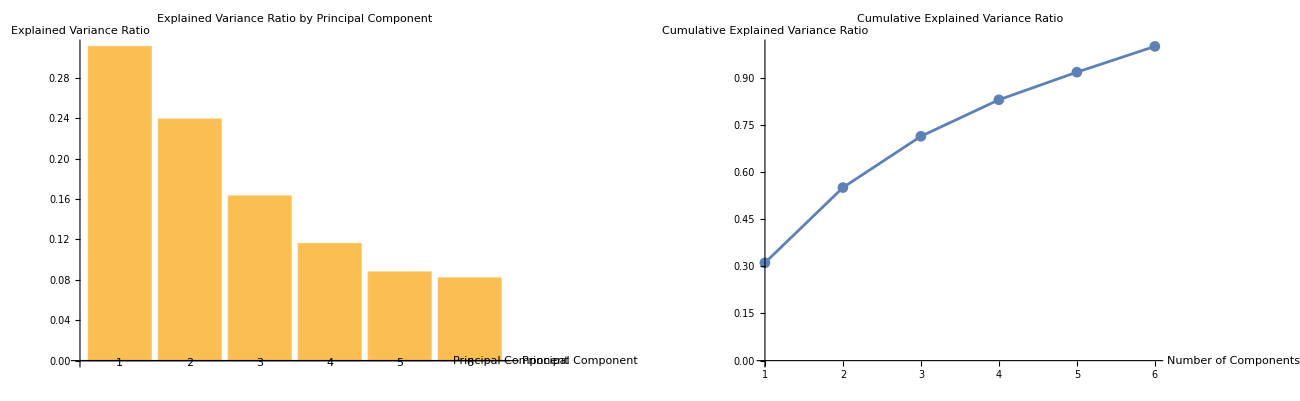

Principal Component | % Variance Explained
1 | 31.1285
2 | 23.9409
3 | 16.3242
4 | 11.6125
5 | 8.79076
6 | 8.20308

```mathematica
(*PCA for top 6 components*)
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],6,Method->"PrincipalComponentsAnalysis"]
reducedPCA=reducerPCA[allPersMeanOfDiff[[All,18]]];
(*Variance Explanation*)
variancesExplained=Variance/@Transpose[reducedPCA];
totalVariance=Total[variancesExplained];
explainedVarianceRatio=variancesExplained/totalVariance;
cumulativeExplainedVarianceRatio=Accumulate[explainedVarianceRatio];
(*Graphing Variance per Component*)
individualVariancePlot=BarChart[explainedVarianceRatio,ChartLabels->Placed[Range[Length[explainedVarianceRatio]],Axis],AxesLabel->{"Principal Component","Explained Variance Ratio"},PlotLabel->"Explained Variance Ratio by Principal Component",ImageSize->300];
cumulativeVariancePlot=ListLinePlot[cumulativeExplainedVarianceRatio,PlotMarkers->Automatic,AxesLabel->{"Number of Components","Cumulative Explained Variance Ratio"},PlotLabel->"Cumulative Explained Variance Ratio",PlotRange->{{1,6},{0,1}},Ticks->{Range[6],Automatic},ImageSize->300];
GraphicsGrid[{{individualVariancePlot,cumulativeVariancePlot}}, Spacings->{1,1},ImageSize->1300,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{2,{Automatic,{1->-90}}}]
percentageExplained=100*explainedVarianceRatio;
TableForm[Transpose[{Range[Length[percentageExplained]],percentageExplained}],TableHeadings->{None,{"Principal Component","% Variance Explained"}}]
```

#### Homemade Variance Explained

```mathematica
(*means=Mean/@Transpose[allPersMeanOfDiff[[All,18]]];*)
standardized=Transpose[Standardize/@Transpose[allPersMeanOfDiff[[All,18]]]];
totalVariance=Total[Variance/@Transpose[standardized]];
```

```mathematica
varianceExplainedFromPersonalities[persIndices_]:=Block[
{basisVectors,projected,projectedVariances},
basisVectors=Transpose[standardized[[persIndices]]];
projected=Transpose[Standardize/@Transpose[standardized.basisVectors]];
projectedVariances=Variance/@Transpose[projected];
Total[projectedVariances/totalVariance]
]
```

```mathematica
varianceExplainedFromPersonalities[Range[156]]
```

0.0380859